```mathematica
Image1 =-Graphics-
```

-Graphics-

```mathematica
ImageKeypoints[Image1, {"PixelPosition"}];
```

```mathematica
Image2 =-Graphics-
```

-Graphics-

```mathematica
flow = ImageDisplacements[{Image1, Image2},MaxIterations->500];
```

```mathematica
Image[Rescale[flow⟦1⟧]]
```

-Graphics-

```mathematica
Dimensions[flow]
hers = Partition[Flatten[flow], {2}];
```

{1,240,320,2}

```mathematica
{hers[[All,1]], hers[[All,2]]}
```

{{3.91173×10^-6,9.11815×10^-6,0.0000156911,0.0000158893,-2.91512×10^-6,-0.0000456034,-0.000102085,-0.000158396,-0.000203647,-0.000224684,-0.00020882,-0.000155909,-0.0000860391,-0.0000293401,-3.7722×10^-6,-6.16548×10^-6,76768,-0.265891,-0.356019,-0.485136,-0.616779,-0.697892,-0.709117,-0.67625,-0.628404,-0.564833,-0.467899,-0.334388,-0.194724,-0.0907722,-0.0349209,-0.0117067,-0.00363531},{1}}
 |  |  |  |

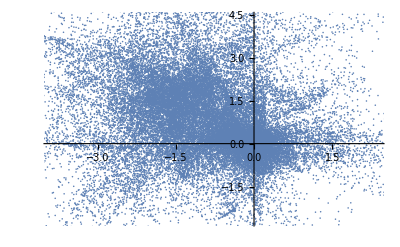

```mathematica
ListPlot[hers]
```

```mathematica
SmoothHistogram3D[hers]
```

-Graphics3D-

```mathematica
herThreshold = FindThreshold[hers] *0.1
```

0.235806

```mathematica
newHers = Threshold[hers,herThreshold] ;
```

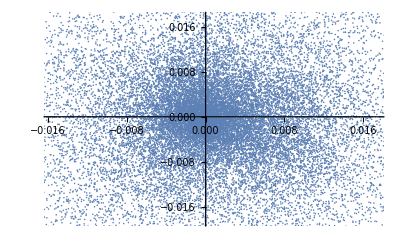

```mathematica
ListPlot[hers - newHers]
```

```mathematica
SmoothHistogram3D[hers - newHers]
```

-Graphics3D-

```mathematica
newAll = (hers - newHers)
```

{{3.91173×10^-6,-3.27514×10^-6},{9.11815×10^-6,-8.28757×10^-6},{0.0000156911,-0.0000136667},{0.0000158893,-0.0000174403},{-2.91512×10^-6,-0.0000213922},{-0.0000456034,-0.0000276908},{-0.000102085,-0.0000319968},{-0.000158396,-0.0000227914},76784,{0.,-0.0253694},{0.,-0.00966217},{0.,-0.00711541},{-0.194724,-0.00961202},{-0.0907722,-0.00880003},{-0.0349209,-0.00501695},{-0.0117067,-0.00176371},{-0.00363531,-0.000246074}}
 |  |  |  |

```mathematica
{Mean[newAll[[All,1]]],Mean[newAll[[All,2]]]}
```

{-0.00129872,0.000636793}

```mathematica
last = ParallelTable[{TrimmedMean[newAll[[All,1]], i], TrimmedMean[newAll[[All,2]], i]},{i,0,0.49,0.01}]; // AbsoluteTiming
```

{26.8657,Null}

```mathematica
SmoothHistogram3D[last]
```

-Graphics3D-

```mathematica
last //MatrixForm
```

(-0.00129872 | 0.000636793
-0.00121657 | 0.000620619
-0.000972904 | 0.000503789
-0.000649918 | 0.000337811
-0.000331514 | 0.000181011
-0.0000661944 | 0.0000527315
0.000103038 | -0.000034626
0.000189389 | -0.0000961183
0.000236144 | -0.000129758
0.000257151 | -0.0001469
0.000264936 | -0.000153796
0.000265418 | -0.000154455
0.000258844 | -0.00015039
0.000245558 | -0.000143832
0.000227692 | -0.0001357
0.000206396 | -0.000127182
0.000184199 | -0.000117845
0.000162299 | -0.000108686
0.000140853 | -0.0000986712
0.000120342 | -0.0000875683
0.000101153 | -0.0000746498
0.000082845 | -0.000061366
0.0000654803 | -0.0000480994
0.0000483385 | -0.000034459
0.0000320142 | -0.0000212483
0.0000170991 | -9.84431×10^-6
6.09794×10^-6 | -2.31171×10^-6
9.47046×10^-7 | -2.74714×10^-8
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.
0. | 0.)

```mathematica
Mean[last]
```

{-0.0000263916,7.90443×10^-6}